```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mLI"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mLI

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

## Equations & Frequencies

```mathematica
w=2π/23.934;
gnval=29.1646943×10^6×2π;
ghgval=7.590118×10^6×2π;
(*B: Tesla, t: hours, f: Hz*)
fr[b_,bp_,gn_,gpn_,p_,t_]:=gn/(2π)b+gpn/(2π)bp Sin[w t+p];
```

```mathematica
Manipulate[Plot[{fr[10^-6,0,ghgval,0,p,t],fr[10^-6,10^-6,ghgval, ghgval,p,t],fr[10^-6,bp 10^-6,ghgval,gphg ghgval,p,t]},{t,0,48},Frame->True,FrameLabel->{"t (hours)","f_Hg (Hz)"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->1000,Axes->None,PlotRange->{{0,48},{-4,20}},PlotStyle->{{Blue,DotDashed},{Gray,Dashed},{Red,Thick}},
PlotLegends->{"f_Hg(B'_0=0,γ'_Hg=0)","f_Hg(B'_0=B_0,γ'_Hg=γ_Hg)","f_Hg(B'_0=bp.B_0,γ'_Hg=gphg.γ_Hg)"},
PlotLabel->StringJoin["{ B_0 , B'_0 } μT = { 1 , ",ToString[N[bp]]," }\n","{ γ_Hg , γ'_Hg } MHz T^-1 = { ",ToString[SetPrecision[N[ghgval/(10^6 2π)],3]] , " , ",ToString[SetPrecision[N[gphg ghgval/(10^6 2π)],3]]," } ;"]],{bp,0,1},{gphg,0,1},{p,0,2π}]
```

```mathematica
Manipulate[Plot[{fr[10^-6,0,gnval,0,p,t],fr[10^-6,10^-6,gnval, gnval,p,t],fr[10^-6,bp 10^-6,gnval,gpn gnval,p,t]},{t,0,48},Frame->True,FrameLabel->{"t (hours)","f_n (Hz)"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->1000,Axes->None,PlotRange->{{0,48},{-4,64}},PlotStyle->{{Blue,DotDashed},{Gray,Dashed},{Red,Thick}},
PlotLegends->{"f_n(B'_0=0,γ'_n=0)","f_n(B'_0=B_0,γ'_n=γ_n)","f_Hg(B'_0=bp.B_0,γ'_n=gpn.γ_n)"},
PlotLabel->StringJoin["{ B_0 , B'_0 } μT = { 1 , ",ToString[N[bp]]," }\n","{ γ_n , γ'_n } MHz T^-1 = { ",ToString[SetPrecision[N[gnval/(10^6 2π)],3]] , " , ",ToString[SetPrecision[N[gpn gnval/(10^6 2π)],3]]," }"]],{bp,0,1},{gpn,0,1},{p,0,2π}]
```

```mathematica
Manipulate[Plot[{fr[10^-6,0,gnval,0,p,t]/fr[10^-6,0,ghgval,0,p,t],fr[10^-6,10^-6,gnval, gnval/2,p,t]/fr[10^-6,10^-6,ghgval, ghgval,p,t],fr[10^-6,bp 10^-6,gnval,gpn gnval,p,t]/fr[10^-6,bp 10^-6,ghgval,gphg ghgval,p,t]},{t,0,48},Frame->True,FrameLabel->{"t (hours)","R = f_n/f_Hg"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->1000,Axes->None,PlotRange->{{0,48},{-4,11}},PlotStyle->{{Blue,DotDashed},{Gray,Dashed},{Red,Thick}},
PlotLegends->{"R(B'_0=0,γ'_n=0)","R(B'_0=B_0,γ'_n=2γ_n,γ'_Hg=γ_Hg)","R(B'_0=bp.B_0,γ'_n=gpn.γ_n,γ'_Hg=gphg.γ_Hg)"},
PlotLabel->StringJoin["{ B_0 , B'_0 } μT = { 1 , ",ToString[N[bp]]," }\n","{ γ_n , γ'_n } MHz T^-1 = { ",ToString[SetPrecision[N[gnval/(10^6 2π)],3]] , " , ",ToString[SetPrecision[N[gpn gnval/(10^6 2π)],3]]," }\n","{ γ_Hg , γ'_Hg } MHz T^-1 = { ",ToString[SetPrecision[N[ghgval/(10^6 2π)],3]] , " , ",ToString[SetPrecision[N[gphg ghgval/(10^6 2π)],3]]," }"]],{bp,0,1},{gpn,0,1},{gphg,0,1},{p,0,2π}]
```

## Asking the question, are we really sensitive to {bp, gphg, gpn} separately? Or to the products: {bp.gphg, bp. gpn}? In essence asking the question is R(t) a 3 parameter equation or a 2 parameter equation? Answer: only sensitive to the products.

```mathematica
Manipulate[Plot[{fr[10^-6,0,gnval,0,p,t]/fr[10^-6,0,ghgval,0,p,t],fr[10^-6,10^-6,gnval, gnval/2,p,t]/fr[10^-6,10^-6,ghgval, ghgval,p,t],fr[10^-6,bp 10^-6,gnval,gpn gnval,p,t]/fr[10^-6,bp 10^-6,ghgval,gphg ghgval,p,t]},{t,0,48},Frame->True,FrameLabel->{"t (hours)","R = f_n/f_Hg"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->1000,Axes->None,PlotRange->{{0,48},{-4,11}},PlotStyle->{{Blue,DotDashed},{Gray,Dashed},{Red,Thick}},
PlotLegends->{"R(B'_0=0,γ'_n=0)","R(B'_0=B_0,γ'_n=2γ_n,γ'_Hg=γ_Hg)","R(B'_0=bp.B_0,γ'_n=gpn.γ_n,γ'_Hg=gphg.γ_Hg)"},
PlotLabel->StringJoin["{ B_0 , B'_0 } μT = { 1 , ",ToString[N[bp]]," }\n","{ γ_n , γ'_n } MHz T^-1 = { ",ToString[SetPrecision[N[gnval/(10^6 2π)],3]] , " , ",ToString[SetPrecision[N[gpn gnval/(10^6 2π)],3]]," }\n","{ γ_Hg , γ'_Hg } MHz T^-1 = { ",ToString[SetPrecision[N[ghgval/(10^6 2π)],3]] , " , ",ToString[SetPrecision[N[gphg ghgval/(10^6 2π)],3]]," }"]],{bp,0,1},{gpn,0,1},{gphg,0,1},{p,0,2π}]
```

## Let us ask the question if Hg sees a different field compared to n? Here

```mathematica
Manipulate[Plot[{fr[10^-6,0,gnval,0,p,t]/fr[10^-6,0,ghgval,0,p,t],fr[10^-6,10^-6,gnval, gnval/2,p,t]/fr[10^-6,10^-6,ghgval, ghgval,p,t],fr[10^-6 b0,bpn 10^-6,gnval,gpn gnval,p,t]/fr[10^-6 b0,bphg 10^-6,ghgval,gphg ghgval,p,t]},{t,0,48},Frame->True,FrameLabel->{"t (hours)","R = f_n/f_Hg"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->1000,Axes->None,PlotRange->{{0,48},{-4,11}},PlotStyle->{{Blue,DotDashed},{Gray,Dashed},{Red,Thick}},
PlotLegends->{"R(B'_0=0,γ'_n=0)","R(B'_0=B_0,γ'_n=2γ_n,γ'_Hg=γ_Hg)","R(B'_0=bp.B_0,γ'_n=gpn.γ_n,γ'_Hg=gphg.γ_Hg)"},
PlotLabel->StringJoin["{ B_0 , B'_n , B'_Hg } μT = { ",ToString[N[b0]]," , ",ToString[N[bpn b0]]," , ",ToString[N[bphg b0]]," }\n","{ γ_n , γ'_n } MHz T^-1 = { ",ToString[SetPrecision[N[gnval/(10^6 2π)],3]] , " , ",ToString[SetPrecision[N[gpn gnval/(10^6 2π)],3]]," }\n","{ γ_Hg , γ'_Hg } MHz T^-1 = { ",ToString[SetPrecision[N[ghgval/(10^6 2π)],3]] , " , ",ToString[SetPrecision[N[gphg ghgval/(10^6 2π)],3]]," }"]],{b0,0.5,1.5},{bpn,0,1},{bphg,0,1},{gpn,0,1},{gphg,0,1},{p,0,2π}]
```

```mathematica
fr[10^-6,bp 10^-6,gnval,gpn gnval,p,t]/fr[10^-6,bp 10^-6,ghgval,gphg ghgval,p,t]
```

(29.1647+29.1647 bp gpn Sin[p+0.262521 t])/(7.59012+7.59012 bp gphg Sin[p+0.262521 t])

## Mercury Comparison

```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

```mathematica
runNum2={11395};
i=1;
dathg=metadat=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum2[[i]],10,6],"\\",IntegerString[runNum2[[i]],10,6],"_Meta3.edm"],metaStructure2];
runn2=Dimensions[dathg][[1]]
ptdathg=Table[{0,{0,0}},{k,1,runn2}];
sttime=AbsoluteTime[dathg[[1]][[1]]];
ghg=1(*7.590118*);
maxhgf=Max[dathg[[;;,20]]]
For[j=1,j≤runn2,j++,
ptdathg[[j]]={(AbsoluteTime[dathg[[j]][[1]]]-sttime)/(24*3600),{dathg[[j]][[20]],dathg[[j]][[21]]}/(ghg*maxhgf)};
];
EDAListPlot[ptdathg,Frame->True,FrameLabel->{"Time (Days)","f_Hg ×7.8 (Hz)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Large}]
```

1047

7.86933

-Graphics-

## FFTs-Sample

```mathematica
ptdathg[[2]][[2]][[1]]
```

0.999999

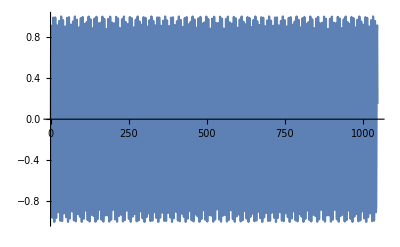

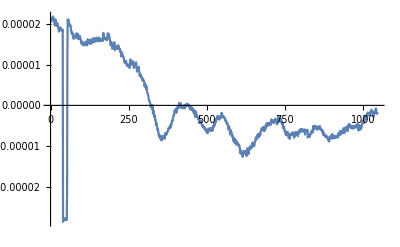

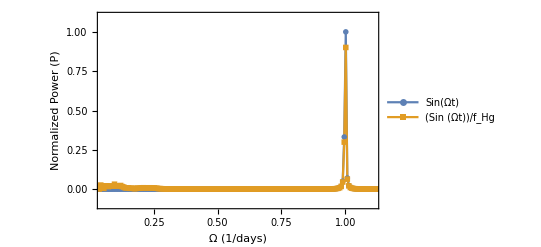

```mathematica
dt2=1;M=runn2;w=1;
timeseries=Table[Sin[w t],{t,0,M-1,dt2}];
(*timeseries2=Table[Sin[w t]/Sin[0.5w t],{t,1,M,dt2}];*)
timeseries2=Table[(ptdathg[[t]][[2]][[1]]-Mean[ptdathg[[;;,2]][[;;,1]]]),{t,1,M,dt2}];
ListPlot[timeseries,Joined->True]
powerspectrum=Abs[Fourier[timeseries]]^2;
(***)
ListPlot[timeseries2,Joined->True]
powerspectrum2=Abs[Fourier[timeseries2]]^2;
(***)
omegavals=Table[2π t/(M×dt2),{t,0,M-1,dt2}];
ListLinePlot[{Transpose[{omegavals,powerspectrum/Max[powerspectrum[[2;;]]]}],Transpose[{omegavals,((powerspectrum2/(Max[powerspectrum2[[2;;]]]))+(powerspectrum/(1.11Max[powerspectrum[[2;;]]])))}]},PlotLegends->{"Sin(Ωt)","(Sin (Ωt))/f_Hg"},PlotRange->{{0.05,1.11},{-.1,1.1}},Frame->True,FrameLabel->{"Ω (1/days)","Normalized Power (P)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Small}]
```